```mathematica
hourlyBostonTemperatureTimeSeriesResample=TimeSeriesResample[WeatherData["KBOS","Temperature",{{2012,9,1},{2019,6,31}}],"Hour"]
```

TimeSeries[…]

```mathematica
Export["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\hourlyBostonTemperatureTimeSeriesResample.wxf", hourlyBostonTemperatureTimeSeriesResample]
```

C:\Users\kylem\Documents\GitHub\2019-WSS\Final Project\Drafts\kyle\hourlyBostonTemperatureTimeSeriesResample.wxf

```mathematica
RegularlySampledQ[%]
```

True

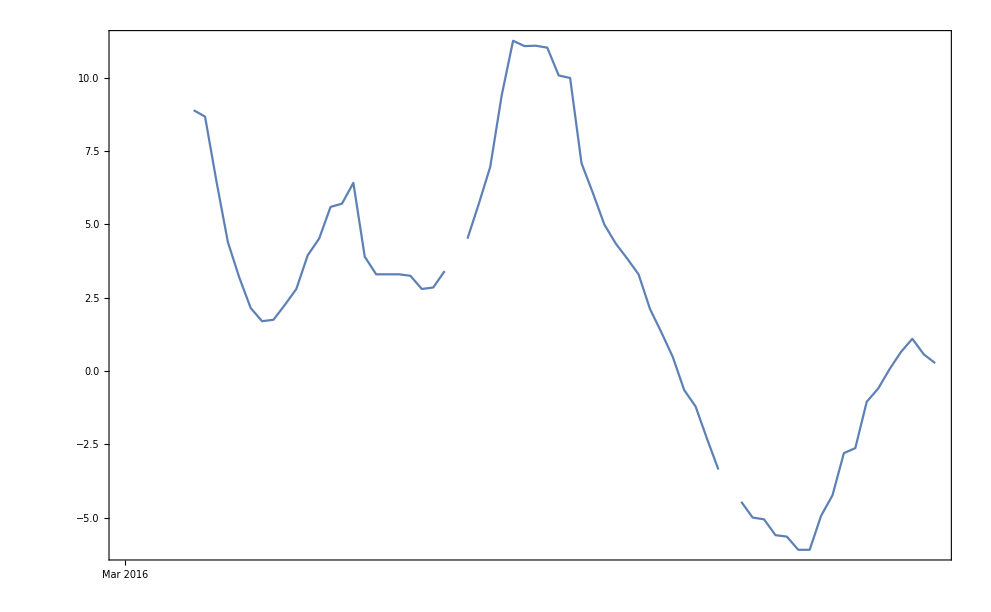

```mathematica
DateListPlot[TimeSeriesWindow[hourlyBostonTemperatureTimeSeriesResample,{DateObject[{2016,3,1}],DateObject[{2016,3,3}]}]]
```